# Mathematica as a Tool for Astronomy and Physics

## Lecture 5 Wintersemester 2009/10 Markus Röllig

## Functions - continuation

### Postfix, Prefix, Infix

Mathematica offers a variety of ways to apply a function to an argument. The standard form is to append the argument in squared brackets appended to the function name:

```mathematica
function[argument]
```

function[argument]

```mathematica
Sin[2 Pi]
```

0

One problem is, that a an argument can again be the function of an argument. You can easily nest many levels of expressions. This makes it sometimes difficult to keep track of opened/closed brackets.

```mathematica
f[f[f[f[f[f[f[x]]]]]]]
```

f[f[f[f[f[f[f[x]]]]]]]

Mathematica tried to assist with interactive syntax highlighting, but the whole expression is still difficult to read and disentangle.

```mathematica
Simplify[Expand[Integrate[x^2+3 x^4-x+2 √x-Log[x],x]]]
```

x+(4 x^(3/2))/3-x^2/2+x^3/3+(3 x^5)/5-x Log[x]

Instead ot enclosing the argument in brackets, you can also use the postfix form, given a function that only depends on a single arguement

```mathematica
f[x]===x//f
```

f[False]

```mathematica
Simplify[(Sin[x]^2-Tan[x]^2)/Cosh[x]^2]===(Sin[x]^2-Tan[x]^2)/Cosh[x]^2//Simplify
```

False

```mathematica
TableForm[Table[{i,i^2,i^3,i^4,i^5},{i,1,10}]]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125
6 | 36 | 216 | 1296 | 7776
7 | 49 | 343 | 2401 | 16807
8 | 64 | 512 | 4096 | 32768
9 | 81 | 729 | 6561 | 59049
10 | 100 | 1000 | 10000 | 100000

```mathematica
Table[{i,i^2,i^3,i^4,i^5},{i,1,10}]//TableForm
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125
6 | 36 | 216 | 1296 | 7776
7 | 49 | 343 | 2401 | 16807
8 | 64 | 512 | 4096 | 32768
9 | 81 | 729 | 6561 | 59049
10 | 100 | 1000 | 10000 | 100000

Another nice way of writing a function is the Prefix form

```mathematica
f[x]===f@x
```

True

This is especially handy, if you want to apply a function to a lengthy argument, because there is no need to scroll to the end of the expression to close the brackets.

```mathematica
Sort@RandomInteger[1000,100]
```

{1,7,26,39,39,49,53,57,78,94,103,108,119,119,132,135,140,153,156,160,164,165,169,170,185,191,253,263,265,277,278,282,302,327,362,365,405,446,448,459,465,487,504,524,528,544,562,564,577,593,602,610,628,630,646,657,657,668,678,683,683,685,689,690,691,717,726,727,728,737,744,746,749,756,762,769,793,811,818,818,820,840,856,862,885,897,898,898,905,912,913,936,939,948,952,962,963,968,988,999}

The Pre- and Postfix form can be combined and also used in a chain

```mathematica
f@g@h@x
```

f[g[h[x]]]

```mathematica
h@x//g//f
```

f[g[h[x]]]

The Infix form can be used with functions of several variables

Infix[f[e_1,e_2,…]] prints with f[e_1,e_2,…] given in default infix form: e_1~f~e_2~f~e_3….

```mathematica
x~f~y
```

f[x,y]

```mathematica
Infix[head[a,b,c,d]]
```

a ~head~ b ~head~ c ~head~ d

```mathematica
Postfix[f[x]]
Prefix[f[x+y]]
```

x//f

f@(x+y)

```mathematica
N@Cos@45
Cos[45] //N
```

0.525322

0.525322

#### Excercise

The Prefix and Infix forms can only be used when the function you want to apply works with a single argument. Give an example of a Post/Prefix application with functions of two or more arguments

Create a 5x5 matrix using the Table command and assign it to a variable. Show the matrix in TableForm, MatrixForm and as Grid, using the Postfix formalism

### Pure Functions

Required Reading:

Pure Functions
Variables in Pure Functions and Rules

If you define a function using the standard assignment f[arg_]:=some_definition you create a function and give it a name (namely f). In some circumstances it is not necessary to give an assignment particular name because e.g. you only need it once. This can be done using Function[x,body], which defines a a pure function in which x is replaced by any argument you provide.

```mathematica
Function[x,1+2 x +x^2]
```

Function[x,1+2 x+x^2]

To apply this function to a variable use any of the discussed ways (Postfix, Infix, Prefix, ....

```mathematica
Function[x,1+2 x +x^2][y]
```

1+2 y+y^2

```mathematica
Function[x,1+2 x +x^2]@y
```

1+2 y+y^2

```mathematica
y//Function[x,1+2 x +x^2]
```

1+2 y+y^2

Giving this Function a name is equivalent to our standard function definition

```mathematica
f=Function[x,1+2 x +x^2];
```

```mathematica
f[10]
```

121

```mathematica
f@10
```

121

Practically there is no need to explicitely name the arguments either. The shorthand notation for Function is (function of #)&

```mathematica
Function[x,1+2 x +x^2]
```

Function[x,1+2 x+x^2]

```mathematica
(1+2#+#^2)&
```

1+2 #1+#1^2&

```mathematica
(1+2#+#^2)&[y]
```

1+2 y+y^2

# represents the first argument supplied to a pure function. #n represents the n-th argument. Hence a pure function of several arguments looks like:

```mathematica
Function[{x,y},x^2+y^2]
```

Function[{x,y},x^2+y^2]

```mathematica
(#1^2+#2^2)&
```

#1^2+#2^2&

Pure functions in Mathematica can take any number of arguments. You can use ## to stand for all the arguments that are given, and ##n to stand for the n^th and subsequent arguments.

##  stands for all arguments.

```mathematica
f[##, ##] &[x, y]
```

1+2 x+x^2

##2 stands for all arguments except the first one

```mathematica
f[##2,#1]&[a,b,c,ap,bp]
```

1+2 b+b^2

Pure functions fully shine when we encounter Mathematica commands like Apply, Map, Thread, etc.

Pure functions can also be used to use the postfix form with functions of more than one parameter.

Imagine a given list which we want to Flatten only at level 1 using the postfix form.

```mathematica
Clear[list]
list={a,b,{{c,c,c}},d,{1,2,3,4{a1,a2},5},{{{{aef1,aef3}}}},e,f}
```

{a,b,{{c,c,c}},d,{1,2,3,{4 a1,4 a2},5},{{{{aef1,aef3}}}},e,Function[x,1+2 x+x^2]}

Using the single-argument form of Flatten, gets rid of all sub-levels

```mathematica
list//Flatten
```

{a,b,c,c,c,d,1,2,3,4 a1,4 a2,5,aef1,aef3,e,Function[x,1+2 x+x^2]}

But we can set up a pure function to provide Flatten with the level argument:

```mathematica
list//Flatten[#,1]&
```

{a,b,{c,c,c},d,1,2,3,{4 a1,4 a2},5,{{{aef1,aef3}}},e,Function[x,1+2 x+x^2]}

```mathematica
Clear[list]
```

#### Excercise

Create a linear pure function and calculate the result for a few arguments.

Create a pure functional polynomial of degree 3 and calculate it for a few arguments

Create the pure function pendant of f[x_, y_] := xy + x Sqrt[x + y]-y^2

Create a pure function that takes a list as argument and returns the second element.

Create a pure function that takes a vector as argument and returns its norm.

Create a pure function that takes two vectors of the same dimension as arguments and returns their scalar product. Create asecond pure function that returns the vector product.

### Attributes

Required Reading:

Attributes

Any Mathematica symbol can also have a variaty of independently set table attributes that define overall aspects of its behavior.

To find the attributes of a symbol/function use the command Attributes

As an example we look at the attributes of the function Plus.

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

#### Flat

Plus has the attribute Flat, which is equivalent to associativity, i.e. it makes:

```mathematica
Plus[1,2,Plus[Plus[3,4],5]]==Plus[1,2,3,4,5]
```

True

or a+(b+c) = a+b+c. All nesting will be flattened out.

#### Orderless

The attribute Orderless, makes f[a,b][ equivalent to f[b,a]. This is the law of commutativity and of course Plus[1,2] should be equal to Plus[2,1]

```mathematica
Plus[1,2]==Plus[2,1]
```

True

#### Listable

The attribute Listable is very important, because it is an attribute that can be assigned to a symbol f to indicate that the function f should automatically be threaded over lists that appear as its arguments.

Listable functions are effectively applied separately to each element in a list, or to corresponding elements in each list if there is more than one list. Most built-in mathematical functions are Listable.

For example Sin is listable

```mathematica
Attributes[Sin]
```

{Listable,NumericFunction,Protected}

```mathematica
Sin[{0,Pi,2Pi}]
```

{0,0,0}

#### NumericFunction

NumericFunction is an attribute that can be assigned to a symbol f to indicate that f[arg_1,arg_2,…] should be considered a numeric quantity whenever all the arg_i are numeric quantities.

```mathematica
NumericQ[Plus[1,2,3]]
```

True

```mathematica
Remove[f]
f[x__]:=Plus[x]
```

```mathematica
NumericQ[f[{1,2,3}]]
```

False

```mathematica
Remove[f]
```

#### OneIdentitiy

OneIdentity is an attribute that can be assigned to a symbol f to indicate that f[x], f[f[x]], etc. are all equivalent to x for the purpose of pattern matching.

```mathematica
Plus[1]==1
```

True

#### Protected

Protected is an attribute which prevents any values associated with a symbol from being modified.Many built-in Mathematica functions have the attribute Protected.

```mathematica
Remove[Plus]
```

Remove::rmptc: Symbol Plus is Protected and cannot be removed.

#### Other important attributes

There are more attributes. Very important is the attribute HoldAll, which specifies that all arguments to a function are to be maintained in an unevaluated form.

Hold is a container with the attribute HoldAll:

```mathematica
Attributes[Hold]
```

{HoldAll,Protected}

```mathematica
Hold[1+2]
```

Hold[1+2]

#### SetAttributes, ClearAttributes

SetAttributes[s,attr]adds attr to the list of attributes of the symbol s.

```mathematica
SetAttributes[f,HoldAll]
```

This will prevent the Mathematica from evaluating the arguments provided to f

```mathematica
f[1+2]
```

f[1+2]

You can also give a list of attributes to set:

```mathematica
SetAttributes[plus,{Flat,Orderless}]
```

```mathematica
plus[a,plus[c,b]]
```

plus[a,b,c]

```mathematica
Remove[plus,f]
```

To remove attributes use ClearAttributes[s,attr]

### Example: Law of cosines example

Taken from Thomas H. Meyer, Department of Natural Resources and the Environment
University of Connecticut thomas.meyer@uconn.edu

#### Law of cosines example

This is a somewhat more complicated, and probably more useful, example based on the planar law of cosines:
cos[θ]==(a^2+b^2-c^2)/(2a b)

In "practice," the LOC can reasonably be used given the angle and two sides from which the third side is to be found, or given three sides from which the angle is to be found. Let's write a single function to do all of that.

This definition automatically determines that we're looking for the angle given three sides

```mathematica
LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=ArcCos[(a^2+b^2-c^2)/(2a b)]
```

```mathematica
LOC[α,50,60,70.]/°
```

78.463

This definition automatically determines that we're looking for the side opposite the angle given the adjacent sides and the angle

```mathematica
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=√(-2a b Cos[θ]+b^2+a^2)
```

```mathematica
LOC[78.463°,60,70.,c]
```

82.5833

We can do the algebra for all four cases, but Mathematica solve the equation for us

```mathematica
Remove[LOC]
LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),θ]
LOC[θ_?NumericQ,a_Symbol,b_?NumericQ,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),a]
LOC[θ_?NumericQ,a_?NumericQ,b_Symbol,c_?NumericQ]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),b]
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),c]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-1.36944},{α→1.36944}}

{{c→-82.5833},{c→82.5833}}

This is cool, but the rules and the negative roots are annoying. Also, let's use a single function rather than repeat the Solve four times

```mathematica
Remove[LOC]
LOCBase[θ_,a_,b_,c_,var_Symbol]:=Max[var/.Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),var]]

LOC[θ_Symbol,a_?NumericQ,b_?NumericQ,c_?NumericQ]:=LOCBase[θ,a,b,c,θ]
LOC[θ_?NumericQ,a_Symbol,b_?NumericQ,c_?NumericQ]:=LOCBase[θ,a,b,c,a]
LOC[θ_?NumericQ,a_?NumericQ,b_Symbol,c_?NumericQ]:=LOCBase[θ,a,b,c,b]
LOC[θ_?NumericQ,a_?NumericQ,b_?NumericQ,c_Symbol]:=LOCBase[θ,a,b,c,c]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,a,50.,50]
LOC[78.463°,60,b,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.36944

20.0001

50.0001

82.5833

One last refinement: have Mathematica find the symbol for us. The braces around var take care of Select always returning a list.

```mathematica
Remove[LOC]
LOCBase[θ_,a_,b_,c_,{var_Symbol}]:=Max[var/.Solve[Cos[θ]==(a^2+b^2-c^2)/(2a b),var]]

LOC[θ_,a_,b_,c_]:=LOCBase[θ,a,b,c,Select[{θ,a,b,c},Head[#]===Symbol&]]
```

```mathematica
LOC[α,50,60,70.]
LOC[78.463°,a,50.,50]
LOC[78.463°,60,b,70.]
LOC[78.463°,60,70.,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.36944

20.0001

50.0001

82.5833

### Excercises

#### Reverse integer

Write and test a function whose effect upon an integer is to reverse its digits.  For example, the input 123 should produce output 321.  Be sure to account for the sign.

#### Apocalyptic numbers

In numerology, a number of the form 2^n that contains the beast number 666 among its sequence of decimal digits is known as an apocalyptic number.  Write a simple procedure that lists the first m exponents that generate apocalyptic numbers.  What are the first 10 apocalyptic numbers?

#### Making change

Write a function that determines the number of coins of each domination needed to provide a specified amount of change using the smallest number of coins.  The output should be a list of pairs containing the number of coins and its denomination.  For example, the change for 0.87 would be {{3,0.25},{1,0.1},{0,0.05},{2,0.01}}.  Begin with standard U.S. denominations, namely, {0.25,0.1,0.05,0.01}, and then generalize to an arbitrary list of denominations.

#### How many circular primes are there below one million?

The number, 197, is called a circular prime because all rotations of the digits: 197, 971, and 719, are themselves prime.

There are thirteen such primes below 100: 2, 3, 5, 7, 11, 13, 17, 31, 37, 71, 73, 79, and 97.

How many circular primes are there below one million?

#### How many reversible numbers are there below one-billion?

Some positive integers n have the property that the sum [ n + reverse(n) ] consists entirely of odd (decimal) digits. For instance, 36 + 63 = 99 and 409 + 904 = 1313. We will call such numbers reversible; so 36, 63, 409, and 904 are reversible. Leading zeroes are not allowed in either n or reverse(n).

There are 120 reversible numbers below one-thousand.
How many reversible numbers are there below one-billion (109)?

## Application Example: LTE approximation

A very common task in radio astronomy is to estimate column densities and temperatures from observations of the interstellar medium. One of the easiest approaches to do so is to assume local thermodynamical equilibrium (LTE). A system is not in local thermodynamic equilibrium if the local kinetic (Maxwellian) temperature is not equal to the Planckian temperature of the radiation field.

The species we will model is carbon monoxide.CO is a linear rotator

```mathematica
(*CGS[PlanckConstant]
CGS[BoltzmannConstant]
CGS[SpeedOfLight]*)
h:=6.62607*10^-27;
k:=1.38065*10^-16;
cl:=2.99792458×10^10;
B12CO:=57.63597*10^9; (* rot constant*)
A10:=7.2036×10^-8; 
aJ[J_,A10_]:=(3 J^4)/(2J+1)A10; (* Einstein A values *)
ν[J_,B_]:=B*J*(J+1);  (* frequency J->0 *)
Δν[jUp_,B_]:=B*jUp*2; (* frequency J->J-1 *)
g[J_]:=2*J+1;  (* statistical weights *)
Energy[J_,B_]:=h*ν[J,B]/k; (* energy of level J *)
```

Allowed transitions are of type J→J±1. 
The partition function is the sum over all levels. Let's sum the first 50 J levels

```mathematica
zusum[T_,B_]:=∑_(i=0)^50 g[i]*ⅇ^((-Energy[i,B])/T);
```

```mathematica
population[i_,T_,B_]:=(g[i]*ⅇ^((-Energy[i,B])/T))/zusum[T,B];
```

With increasing temperature, the upper levels are populated and the lower levels are depopulated.

```mathematica
Table[population[0,i 5,B12CO],{i,1,10}](*ground level*)
```

{0.458211,0.252014,0.173343,0.132044,0.106622,0.0894036,0.0769709,0.0675728,0.0602194,0.0543091}

```mathematica
Table[population[4,i 5,B12CO],{i,1,10}](*level J=4*)
```

{0.0000645834,0.0089758,0.039032,0.0747591,0.104967,0.127272,0.142598,0.152534,0.158515,0.161658}

We see the Boltzmann distribution:

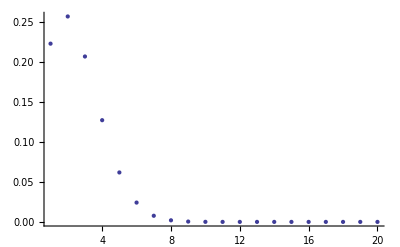

```mathematica
ListPlot[Table[population[i,30,B12CO],{i,1,20}]]
```

Now we want to try and model the emission of such a gas. We need to know the optical depth of a given column of gas with temperature T. 
τ=∫n(l)κ(l)ⅆl,  κ, the absorption coefficient of transition i→i-1 depends on the population of level i and i-1.

```mathematica
κRot[T_,B_,jUp_,A_]:=cl^2/(8π Δν[jUp,B]^2)aJ[jUp,A](g[jUp]/g[jUp-1] population[jUp-1,T,B]-population[jUp,T,B]) cl/(Δν[jUp,B] 10^5);
```

```mathematica
τRot[T_,B_,jUp_,l_,Δv_,nCO_,A_]:=∫_0^l (nCO κRot[T,B,jUp,A])/Δv ⅆx;
```

Now we can calculate the emission in units of main beam temperature:

```mathematica
tMainBeamRotLTE[T_,B_,jUp_,l_,Δv_,nCO_]:=h/k Δv Δν[jUp,B](Exp[(h Δν[jUp,B])/(k T)]-1)^-1(1-Exp[-τRot[T,B,jUp,l,Δv,nCO,aJ[jUp,A10]]]);(* K km s^-1 , Δv is the line width in km/s *)
```

```mathematica
tMainBeamRotLTE[30,B12CO,1,10^17,1,1]
```

24.5171

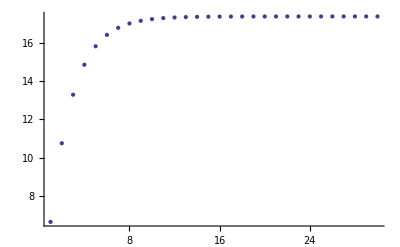

```mathematica
ListPlot@Table[Evaluate@tMainBeamRotLTE[20,B12CO,1,i*10^16,1,1],{i,1,30}]
```

## Graphic Fundamentals

Required Reading

The Structure of Graphics and Sound
The Structure of Graphics
Symbolic Graphics Language
Graphics Directives

### 2-dim Graphics Primitives

Required Reading

Graphics Objects
Styles and Fonts in Output

The basic idea is that Mathematica represents all graphics in terms of a collection of graphics primitives. The primitives are objects like Point, Line and Polygon, that represent elements of a graphical image, as well as directives such as RGBColor and Thickness.

All graphical objects consist of only a few basic constructs, so-called primitives: points, lines (and arrows), polygons (and rectangles), circles (and disks), and text. The Mathematica commands are:
Point[coords] is a graphics primitive that represents a point.
Line[{pt_1,pt_2,…}]is a graphics primitive which represents a line joining a sequence of points.
Polygon[{pt_1,pt_2,…}]is a graphics primitive that represents a filled polygon. 
Circle[{x,y},r]is a two-dimensional graphics primitive that represents a circle of radius r centered at the point x, y. 
Disk[{x,y},r]is a two-dimensional graphics primitive that represents a filled disk of radius r centered at the point x, y.

Text[expr,coords]is a graphics primitive that displays the textual form of expr centered at the point specified by coords.
To change the format and style of the text use the command Style[expr,options]to print with the specified style options

Rectangle[{x_min,y_min},{x_max,y_max}]is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes.

A line from {0,0} to {1,1} is represented as:

```mathematica
Line[{{0,0},{1,1}}]
```

Line[{{0,0},{1,1}}]

To actually draw a line we use the command Graphics[primitives,options], which represents a two-dimensional graphical image.

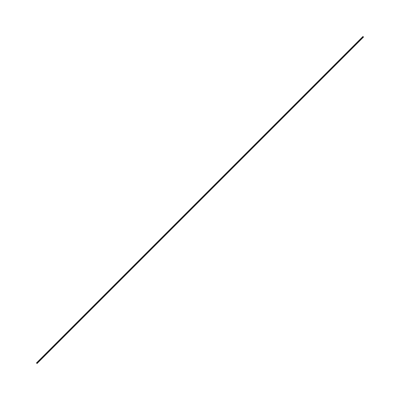

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

```mathematica
FullForm[%]
```

Graphics[Line[List[List[0,0],List[1,1]]]]

```mathematica
InputForm[%%]
```

Graphics[Line[{{0, 0}, {1, 1}}]]

We can control the style of the primitives by giving explicit styling directives. If we want to draw the line Red and Thick

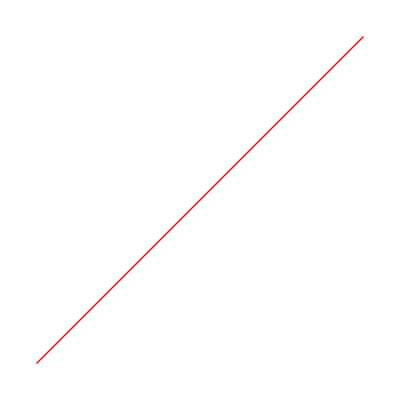

```mathematica
Graphics@{Red,Thick,Line[{{0,0},{1,1}}]}
```

Note, that the outer list groups the graphics directives and the primitves together. Outside the list the standard format is again applied.

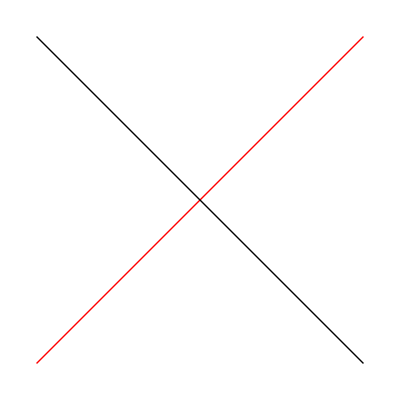

```mathematica
Graphics@{{Red,Thick,Line[{{0,0},{1,1}}]},Line[{{0,1},{1,0}}]}
```

A more complicated example. Within the list the graphics directive is applied until a new directive is found.

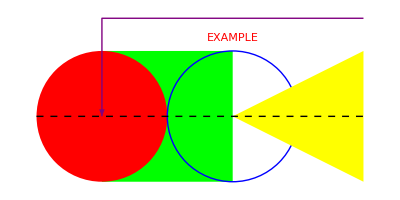

```mathematica
Graphics[
{Thick,Green,Rectangle[{0,-1},{2,1}],
Red,Disk[],
Blue,Circle[{2,0}],
Yellow,Polygon[{{2,0},{4,1},{4,-1}}],
Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],
Black,Dashed,Line[{{-1,0},{4,0}}],
Style[Text["EXAMPLE",{2,1.2}],Italic,Red,Underlined]
}]
```

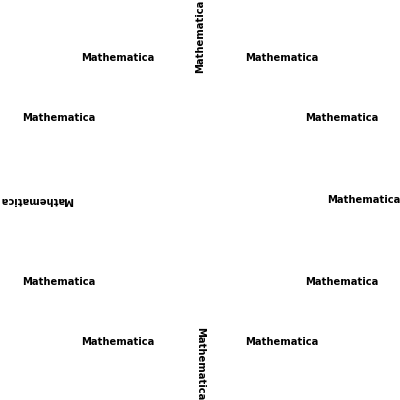

```mathematica
Show[Graphics[{Table[Text[Style["Mathematica",FontFamily->"Helvetica",FontWeight->"Bold",FontSize->10],{Cos[φ],Sin[φ]} 1.5,{0,0},{Cos[φ],Sin[φ]}],{φ,0,2Pi-2Pi/12,2Pi/12}]}]]
```

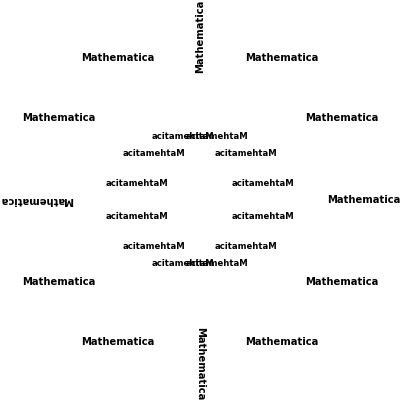

```mathematica
Show[Graphics[{Table[Text[Style["Mathematica",FontFamily->"Helvetica",FontWeight->"Bold",FontSize->10],{Cos[φ],Sin[φ]} 1.5,{0,0},{Cos[φ],Sin[φ]}],{φ,0,2Pi-2Pi/12,2Pi/12}],
Table[Text[Style["acitamehtaM",FontFamily->"Helvetica",FontWeight->"Bold",FontSize->8.5],{Cos[φ],Sin[φ]} 0.6,{0,0},{Cos[φ],Sin[φ]}],{φ,2Pi/24,2Pi-2Pi/24,2Pi/12}]}]]
```

Circles at random positions:

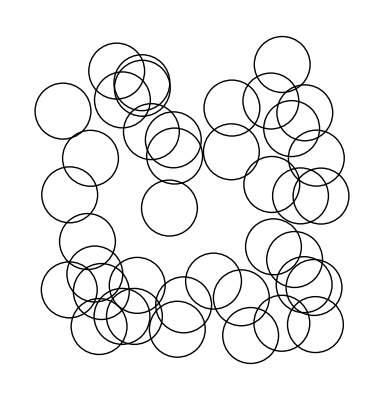

```mathematica
Graphics[Circle/@RandomReal[10,{40,2}]]
```

#### Example

The following function mirrors a point on a given line (why?)

```mathematica
mirror[p_, {p1_, p2_}] := (* mirrors p on line p1p2 *)
        Function[{d, e}, p1 - d + 2(d.e) e][
                           p - p1, (#/Sqrt[#.#])&[p2 - p1]];
```

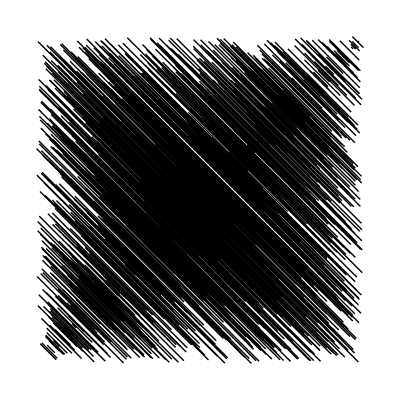

```mathematica
Graphics@(Line/@Map[{#,mirror[#,{{0.,0.},{1.,1.}}]}&,RandomReal[{-1,1},{1000,2}]])
```

#### Excercise

Draw an equilateral triangle with visible points at the corners and lines connecting them.

Put labels a,b,c at the edges and α,β,γ in the corners to denote the angles.
(you can also draw circular arc in the corners).

Construct and display a triangle using the base line running from point p1={0,0} to p2={1,0} and the ratio r=1-x3.

Repeat the above construction for any base line running from arbitrary p1, p2.

Given the above triangle construction visualize the Pythagorean theorem, i.e. draw the corresponding rectangles on the both cathedes.

-Graphics-

Use the above to form an iterative procedure to draw similar triangle/square constructions on the sides of the square opposite the first triangle. If you repeat this over and over again you get the so called trees of Pythagoras.

### Directives

Mathematica allows you detailed control over the way that graphics objects are rendered. Here we present some of the most important ones.

#### Colors

Mathematica knows the following named colors:
Red  ▪  Green  ▪  Blue  ▪  Black  ▪  White  ▪  Gray  ▪  Cyan  ▪  Magenta  ▪  Yellow  ▪  Brown  ▪  Orange  ▪  Pink  ▪  Purple. Additionally you can use the lighter versions, e.g. LightRed, or LightBlue. Another 'color' is Transparent, which represents perfect transparency in graphics or style specifications. Transparent is equivalent to GrayLevel[0,0].


{-Graphics-,-Graphics-}

```mathematica
{Graphics[{Disk[]}],Graphics[{Transparent,Disk[]}]}
```

Another way to specify a color is Hue[h], a graphics directive which specifies that objects which follow are to be displayed, if possible, in a color corresponding to hue h. Hue[h,s,b]specifies colors in terms of hue, saturation and brightness.

```mathematica
ListAnimate[Table[Graphics[{Hue[i],Disk[]}],{i,0,1,0.05}]]
```

Here is a rough translation Hue <-> color names:

Hue[≈0] | Hue[≈0.15] | Hue[≈0.35] | Hue[≈0.55] | Hue[≈0.75] | Hue[≈1]
red | yellow | green | blue | violet | red

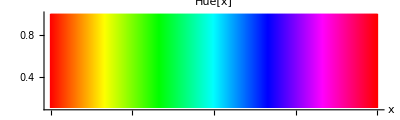

```mathematica
Show[Graphics[
       Table[{Hue[x], Line[{{x, 0.1}, {x, 1}}]}, {x, 0, 1, 0.001}]],
        (* ignore for now *)
     Axes -> {True, False}, AxesOrigin -> {0, 0},
     AspectRatio -> 0.3, AxesLabel -> {"x", None},
     PlotLabel -> StyleForm[Hue[x], "Input", FontFamily -> "Courier"]]
```

Alternatively you can use RGBColor[red,green,blue], a graphics directive which specifies that objects which follow are to be displayed, if possible, in the color given or CMYKColor[cyan,magenta,yellow,black]. GrayLevel[level] is a graphics directive which specifies the gray-level intensity with which objects that follow should be displayed.

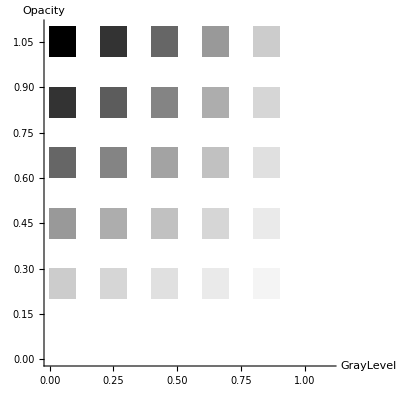

```mathematica
Graphics[ {Table[ {GrayLevel[i,j], Rectangle[{i,j}, {i,j}+0.1]},{i,0,1,0.2}, {j,0,1,0.2}]},Axes->True,AxesLabel->{"GrayLevel","Opacity"}]
```

It is possible to use Lighter, Darker to make colors lighter, darker

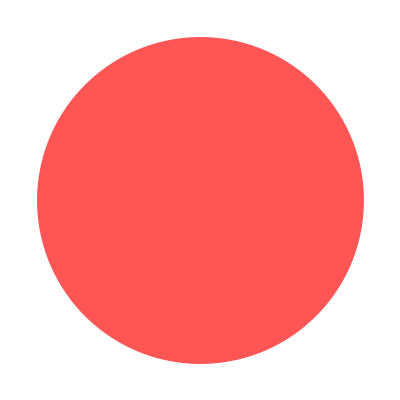

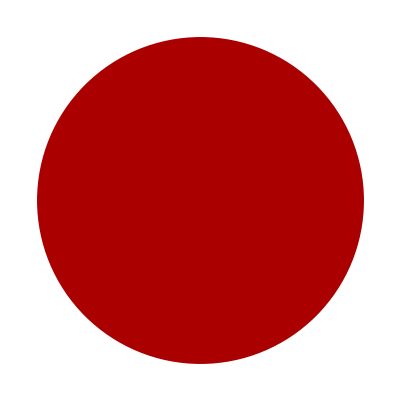

```mathematica
Graphics/@{{Lighter[Red],Disk[]},{Red,Disk[]},{Darker[Red],Disk[]}}
```

Blend[{col_1,col_2,col_3,…},x] linearly interpolates between colors col_i as x varies from 0 to 1.

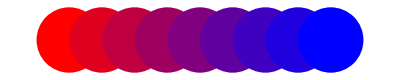

```mathematica
Graphics[Table[{Blend[{Red,Blue},x],Disk[{8x,0}]},{x,0,1,1/8}]]
```

Linear interpolation between colors at specific values:

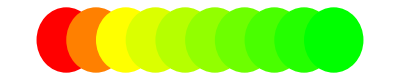

```mathematica
Graphics[Table[{Blend[{{1,Red},{3,Yellow},{10,Green}},x],Disk[{x,0}]},{x,1,10}]]
```

Different colors can be given at the single position to generate discontinuity:

```mathematica
Graphics[Raster[{Range[100]/100},ColorFunction->(Blend[{{0,Red},{1/2,Yellow},{1/2,Green},{1,Blue}},#]&)],AspectRatio->.3]
```

-Graphics-

#### Points

PointSize[d]is a graphics directive which specifies that points which follow are to be shown if possible as circular regions with diameter d. The diameter d is given as a fraction of the total width of the plot.

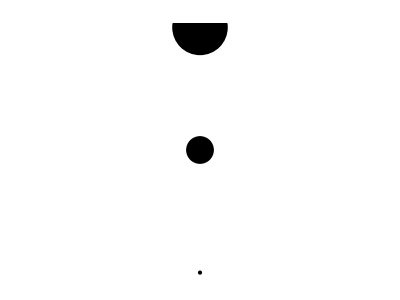

```mathematica
Graphics@{Point[{0,0}],PointSize[0.05],Point[{0,0.25}],PointSize[0.1],Point[{0,0.5}]}
```

AbsolutePointSize[d] is a graphics directive which specifies that points which follow are to be shown if possible as circular regions with absolute diameter d.

```mathematica
Graphics@{Point[{0,0}],AbsolutePointSize[5],Point[{0,0.25}],AbsolutePointSize[10],Point[{0,0.5}]}
```

-Graphics-

#### Lines & Arrows

Thickness[r]is a graphics directive which specifies that lines which follow are to be drawn with thickness r. The thickness r is given as a fraction of the horizontal plot range.

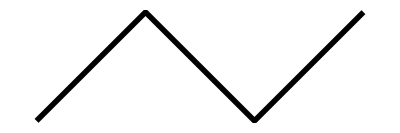
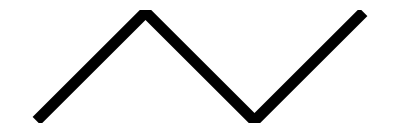
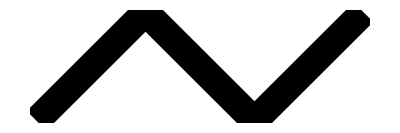

```mathematica
Table[Graphics[{Thickness[r],Line[{{1,0},{2,1},{3,0},{4,1}}]}],{r,{0.01,0.02,0.05}}]
```

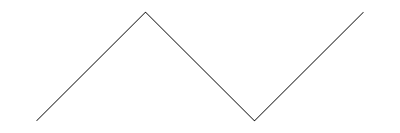
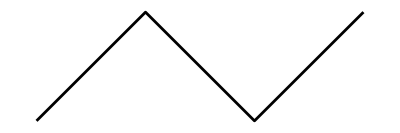
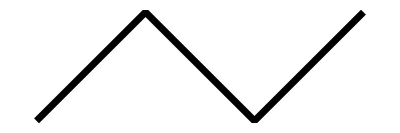

```mathematica
Table[Graphics[{AbsoluteThickness[d],Line[{{1,0},{2,1},{3,0},{4,1}}]}],{d,{0.5,2,5}}]
```

Lines with random thickness:

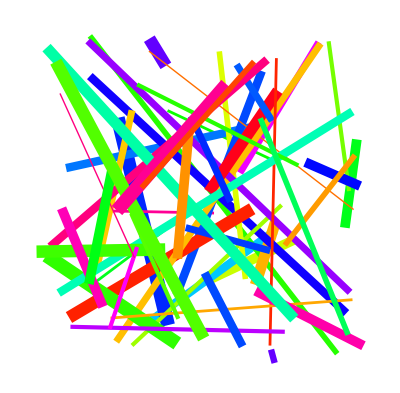

```mathematica
Graphics[Table[{Hue[RandomReal[]],AbsoluteThickness[RandomInteger[{1,10}]],Line[RandomReal[1,{2,2}]]},{50}]]
```

Predefined thicknesses are Thin and Thick.

You can use Dashing[{r_1,r_2,…}]to specifies that lines which follow are to be drawn dashed, with successive segments of lengths r_1, r_2, … (repeated cyclically). The r_i are given as a fraction of the total width of the graph.

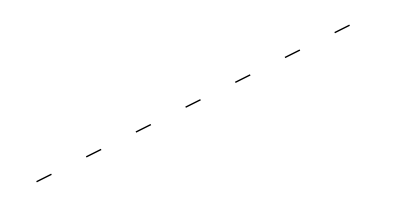
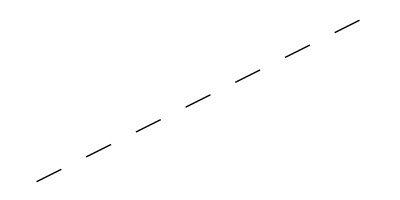
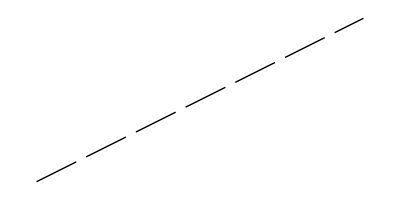
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Dashing[{r,0.1-r}],Line[{{0,0},{2,1}}]}],{r,{0.01,0.03,0.05,0.08}}]
```

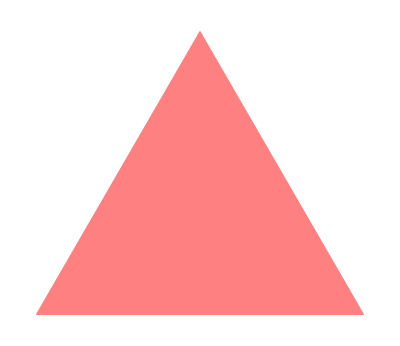
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
p2=Polygon[{{-1,0},{0,Sqrt[3]},{1,0}}];
Table[Graphics[{Pink,EdgeForm[Dashing[r]],p2}],{r,{0.01,0.05,0.1}}]
Clear[p2]
```

Predefined directives include Dashed, Dotted, and DotDashed.

CapForm[type] is a graphics primitive which specifies what type of caps should be used at the ends of lines, tubes and related primitives.
JoinForm[type] is a graphics directive which specifies what type of joins should be used to connect segments of lines, tubes, edges, and related primitives.

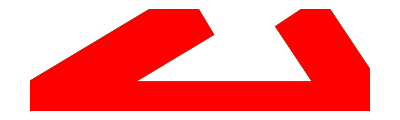

```mathematica
With[{points={{0,0.3},{-0.5,0},{0.5,0},{0.3,0.3}}},Graphics[{Thickness[0.1],{Blue,CapForm["Square"],JoinForm["Miter"],Line[points]},{Green,CapForm["Round"],JoinForm["Round"],Line[points]},{Red,CapForm["Butt"],JoinForm["Bevel"],Line[points]}},PlotRange->1]]
```

Arrowheads[spec]is a graphics directive which specifies that arrows which follow should have arrowheads with sizes, positions and forms specified by spec.

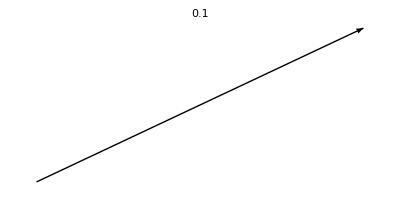
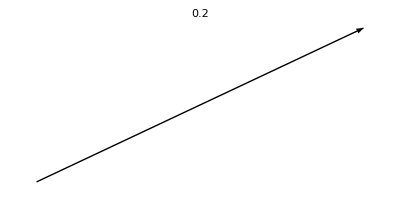
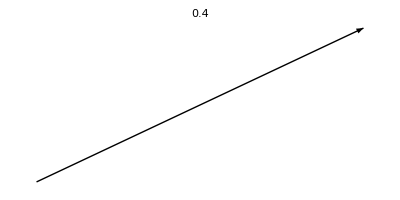

```mathematica
Table[Graphics[{Arrowheads[i],Arrow[{{0,0},{2,1}}]},PlotLabel->i],{i,{.1,.2,.4}}]
```

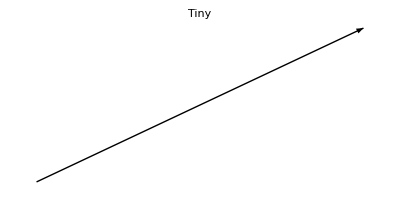
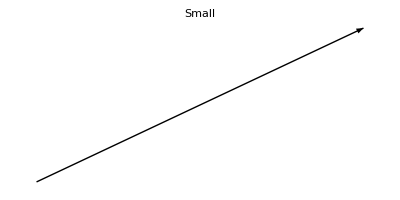
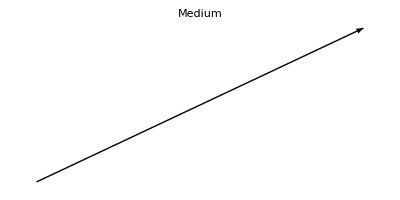
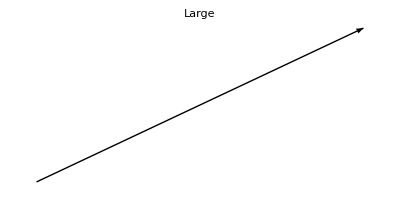

```mathematica
Table[Graphics[{Arrowheads[i],Arrow[{{0,0},{2,1}}]},PlotRange->{{0,2},{0,1}},PlotLabel->i],{i,{Tiny,Small,Medium,Large}}]
```

Double-headed arrow:

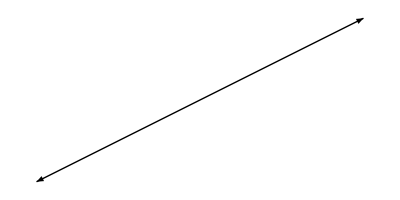

```mathematica
Graphics[{Arrowheads[{-.1,.1}],Arrow[{{0,0},{2,1}}]}]
```

### 3-dim Graphics Primitives

Required Reading

Three-Dimensional Graphics Primitives

Many 2-dim primitives can easiliy be enhance to the third dimensions:
Point[{x,y}]->Point[{x,y,z}]
Line[{{x_1,y_1},{x_2,y_2},…}]->Line[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}]
Arrow[{{x_1,y_1},{x_2,y_2},…}]->Arrow[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}]
Polygon[{{x_1,y_1},{x_2,y_2},…}]->Polygon[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}]
Text[expr,{x,y}]->Text[expr,{x,y,z}]

To create a graphics object from the above primitives, we use Graphics3D (just as in the 2D case).

```mathematica
rcoord:=RandomReal[1.,{3}]
Graphics3D[Table[Point[rcoord],{20}]]
```

-Graphics3D-

The thre dimensional analog of the 2 dimensional shapes are:
 Rectangle -> Cuboid[{x_min,y_min,z_min},{x_max,y_max,z_max}]
 Disk -> Sphere[{x,y,z},r]

```mathematica
Graphics3D[Table[{Cuboid[10 rcoord],Sphere[10 rcoord]},{10}]]
```

-Graphics3D-

```mathematica
Graphics3D[{EdgeForm[Opacity[.3]],Table[{Hue[RandomReal[],.8],Cuboid[{#[[1]],#[[2]],-n}]}&/@Tuples[Range[-n,n],2],{n,0,10}]},Lighting->"Neutral",Boxed->False]
```

-Graphics3D-

Recently new shapes have been added to Mathematica:

Cone[{{x_1,y_1,z_1},{x_2,y_2,z_2}}] a cone with a base radius of 1 centered around {x_1,y_1,z_1} with the point at {x_2,y_2,z_2}
Cone[{{x_1,y_1,z_1},{x_2,y_2,z_2}},r]a cone with a base radius of r
Cylinder[{x_1,y_1,z_1},{x_2,y_2,z_2}]a cylinder of radius 1 with endpoints at {x_1,y_1,z_1} and {x_2,y_2,z_2}
Cylinder[{x_1,y_1,z_1},{x_2,y_2,z_2},r]a cylinder of radius r
Tube[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}]a tube connecting the specified points
Tube[{{x_1,y_1,z_1},{x_2,y_2,z_2},…},r]a tube of radius r

```mathematica
Graphics3D[Cone[]]
```

-Graphics3D-

Cone with different radii:

```mathematica
Graphics3D[{Cone[{{0,0,3},{0,0,-3}},1],Cone[{{5,0,3},{5,0,-3}},3]}]
```

-Graphics3D-

Cone with different directions :

```mathematica
Graphics3D[{Cone[{{0,0,0},{1,0,0}}],Cone[{{1,1,1},{2,3,1}}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{LightBrown,Cone[{{5,0,3},{5,0,-3}},1.5],Brown,Sphere[{4,0,3.5},1],White,Sphere[{6,0,3.5},1],Orange,Sphere[{5,-1,3.5},1],Green,Sphere[{5,0,5},1],Sphere[{5,1,3.5},1]}]
```

-Graphics3D-

New in V7 Mathematica now offers a 3D equivalent to Line, namely Tube. Tube[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}] represents a 3D tube around the line joining a sequence of points.

```mathematica
Graphics3D[{Tube[{{0,0,0},{1,1,1}}],Line[{{0,0,1},{1,1,0}}]}]
```

-Graphics3D-

You can also provide a radius r

```mathematica
Graphics3D[{Tube[{{0,0,0},{1,1,1}},0.03],Line[{{0,0,1},{1,1,0}}]}]
```

-Graphics3D-

Different primitives may be used together. For example we can draw BezierCurve using Tube instead of Line:

```mathematica
Graphics3D[BezierCurve[{{0,0,0},{1,1,1},{2,0,1}}]]
```

-Graphics3D-

```mathematica
Graphics3D[Tube[BezierCurve[{{0,0,0},{1,1,1},{2,0,1}}],.2]]
```

-Graphics3D-

EdgeForm[g]is a graphics directive which specifies that edges of polygons and other filled graphics objects are to be drawn using the graphics directive or list of directives g.

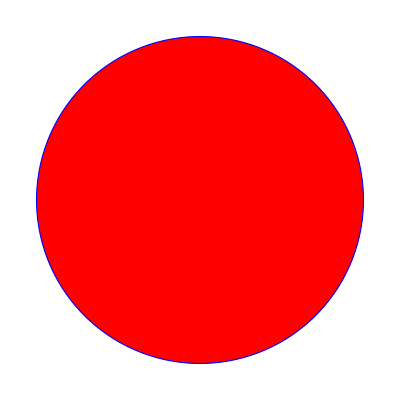

```mathematica
Graphics[{EdgeForm[{Thick,Blue}],Red,Disk[]}]
```

Edges with different thickness:

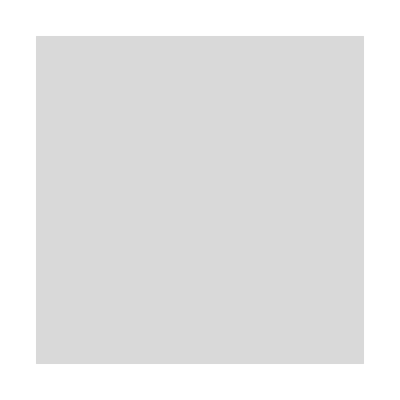
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{EdgeForm[Thickness[t]],LightGray,Rectangle[]}],{t,{Tiny,Small,Medium,Large}}]
```

Edges with different dashing:

```mathematica
Table[Graphics[{EdgeForm[Dashing[d]],LightGray,Rectangle[]}],{d,{Tiny,Small,Medium,Large}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graphics3D[{EdgeForm[{Thick,Blue}],Red,Cuboid[]},Boxed->False]
```

-Graphics3D-

FaceForm[g]is a graphics directive which specifies that faces of polygons and other filled graphics objects are to be drawn using the graphics directive or list of directives g. You can alos draw front and back face differently by specifying: FaceForm[g,gback](FaceForm[] draws no faces. )

```mathematica
Graphics3D[{FaceForm[Yellow,Blue],Cuboid[]},PlotRange->{{-1/4,5/4},{1/4,5/4},{-1/4,5/4}}]
```

-Graphics3D-

### Options for 2-dim Graphics

Required Reading:

Graphics Options & Styling
Options for Graphics

```mathematica
Length[Options[Graphics]]
```

38

```mathematica
First /@ Options[Graphics]
```

{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BaselinePosition,BaseStyle,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,LabelStyle,Method,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PreserveImageOptions,Prolog,RotateLabel,Ticks,TicksStyle}

AspectRatio is an option for Graphics and related functions which specifies the ratio of height to width for a plot. The default used to be 1/GoldenRatio (≈0.62)


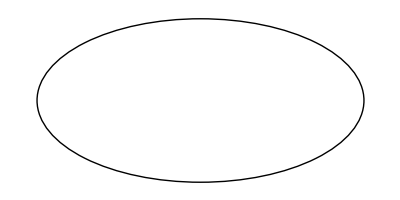
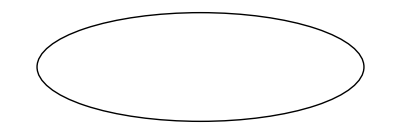

```mathematica
Table[Graphics[Circle[],AspectRatio->1/k],{k,1,3}]
```

Axes is an option for graphics functions that specifies whether axes should be drawn.
AxesLabel is an option for graphics functions that specifies labels for axes. 
AxesStyle is an option for graphics functions which specifies how axes should be rendered.

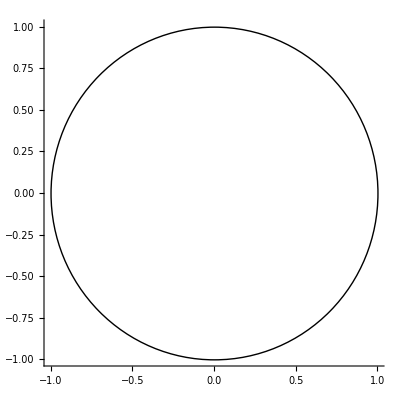

```mathematica
Graphics[Circle[],Axes->True]
```

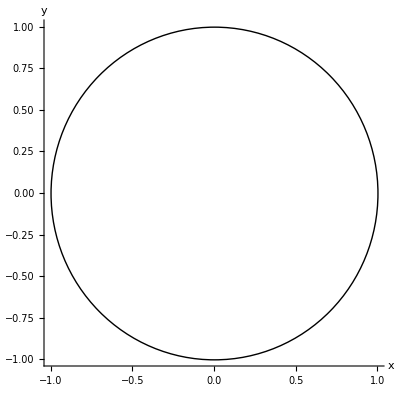

```mathematica
Graphics[Circle[],Axes->True,AxesLabel->{x,y}]
```

```mathematica
Graphics[Circle[],Axes->True,AxesLabel->{x,y},AxesStyle->{Directive[Orange,12],Directive[Blue,15,Italic]}]
```

-Graphics-

Directive[g_1,g_2,…] represents a single graphics directive composed of the directives g_1, g_2, ….

```mathematica
Graphics[Circle[],Axes->True,AxesLabel->{x,y},AxesStyle->{Directive[Orange,12],Directive[Blue,15,Italic]},TicksStyle->{Red,Green}]
```

-Graphics-

Ticks is an option for graphics functions that specifies tick marks for axes. The following settings can be given for Ticks: None, Automatic, {xticks, yticks, …}

GridLines is an option for two-dimensional graphics functions that specifies grid lines.

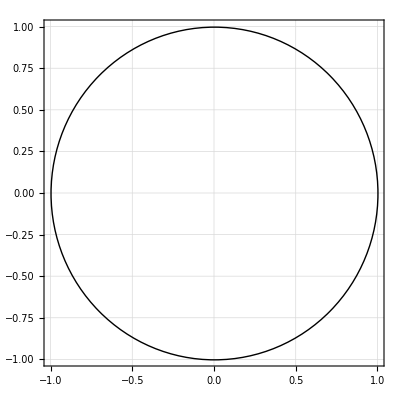

```mathematica
Graphics[Circle[], Frame -> True, GridLines -> Automatic]
```

Specify overall grid lines style, using GridLinesStyle:

```mathematica
Graphics[Circle[],Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed]]
```

-Graphics-

Alternatively you can draw a Frame around your graphic.

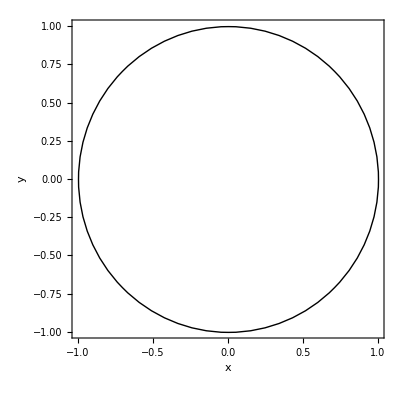

```mathematica
Graphics[Circle[],Axes->False,Frame->True,FrameLabel->{x,y},FrameStyle->{Directive[Orange,12],Directive[Blue,15,Italic]}]
```

Background is an option which specifies what background color to use.

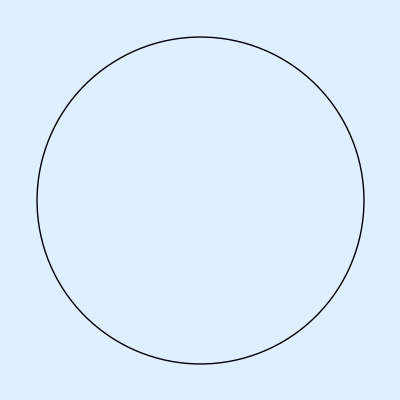

```mathematica
Graphics[{Circle[]},Background->LightBlue]
```

Background can als be used with other commands/styles

```mathematica
Grid[Table[Binomial[n,k],{n,15},{k,15}],Background->{None,{{LightRed,LightBlue}}}]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
5 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0 | 0 | 0 | 0 | 0 | 0
10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1 | 0 | 0 | 0 | 0 | 0
11 | 55 | 165 | 330 | 462 | 462 | 330 | 165 | 55 | 11 | 1 | 0 | 0 | 0 | 0
12 | 66 | 220 | 495 | 792 | 924 | 792 | 495 | 220 | 66 | 12 | 1 | 0 | 0 | 0
13 | 78 | 286 | 715 | 1287 | 1716 | 1716 | 1287 | 715 | 286 | 78 | 13 | 1 | 0 | 0
14 | 91 | 364 | 1001 | 2002 | 3003 | 3432 | 3003 | 2002 | 1001 | 364 | 91 | 14 | 1 | 0
15 | 105 | 455 | 1365 | 3003 | 5005 | 6435 | 6435 | 5005 | 3003 | 1365 | 455 | 105 | 15 | 1

Epilog and Prolog are  options for graphics functions which gives a list of graphics primitives to be rendered after/before the main part of the graphics is rendered.

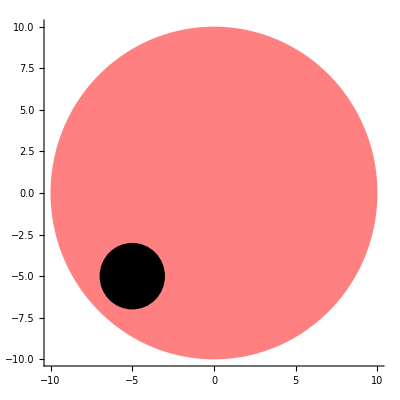
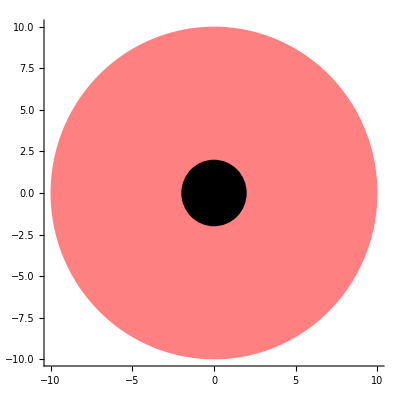
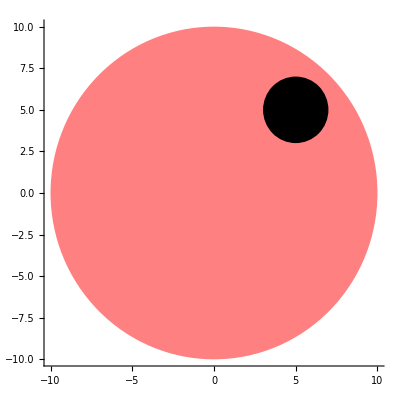

```mathematica
Table[Graphics[{Pink,Disk[{0,0},10]},Axes->True,Epilog->Disk[p,2]],{p,{{-5,-5},{0,0},{5,5}}}]
```

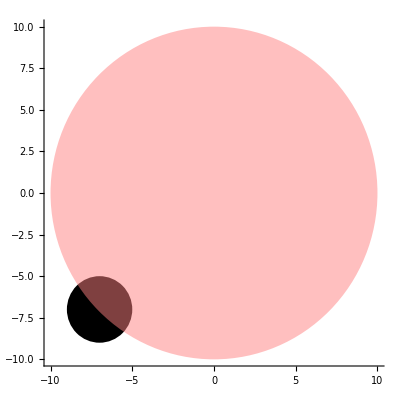
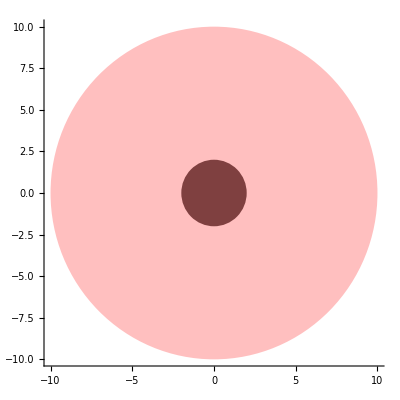
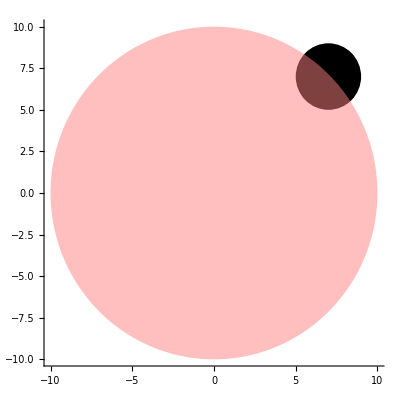

```mathematica
Table[Graphics[{Pink,Opacity[.5],Disk[{0,0},10]},Axes->True,Prolog->Disk[p,2]],{p,{{-7,-7},{0,0},{7,7}}}]
```

A common task for Epilog is to plot data points on top of plots of functions:

```mathematica
data=Table[{i,RandomReal[i]},{i,10}];
```

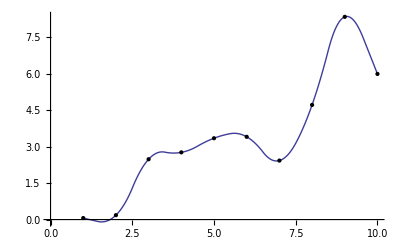

```mathematica
ListLinePlot[data,Epilog->{PointSize[Medium],Point[data]},InterpolationOrder->2]
```

If an option is set more than once, the value used is always the one that was set first.

If you want to redraw a graphic with different options you can use:
Show[graphics,options]shows graphics with the specified options added.

```mathematica
Graphics[Circle[], Frame -> True, GridLines -> Automatic]
```

-Graphics-

```mathematica
Show[%,Frame->False,GridLines->None, Axes->{False,True}]
```

-Graphics-

Another option, not only for 2-dim but also for 3-dim graphics is VertexColors which specifies the colors to assign to vertices. VertexColors can be used with Polygon, Line, Tube, Point and GraphicsComplex. VertexColors->{col_1,col_2,…} specifies that color col_i should be assigned to vertex i. The interior of the polygon is colored by interpolating between the colors specified by VertexColors.

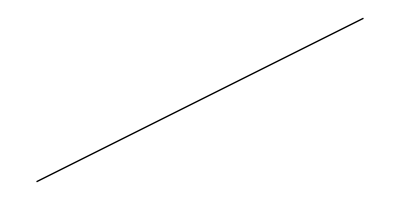

```mathematica
Graphics[{Thick,Line[{{0,0},{2,1}},VertexColors->{Red,Green}]}]
```

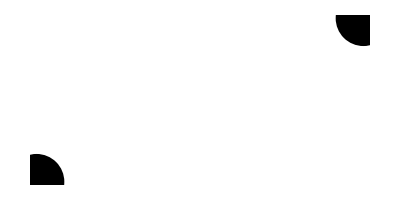

```mathematica
Graphics[{PointSize[0.1],Point[{{0,0},{2,1}},VertexColors->{Red,Green}]}]
```



```mathematica
Graphics[Polygon[{{-1,0},{1,0},{0,Sqrt[3]}},VertexColors->{Red,Green,Blue}]]
```

### 3D Graphics Options

Required reading:

3D Graphics Options
Labeling Three-Dimensional Graphics

Many 2-dim options are also valid for 3-dim graphics. However, 3-dim graphics requires some special options. One example is the viewing geometry,another is the drawing of boxes around the graphics.

ViewPoint is an option for Graphics3D and related functions which gives the point in space from which three-dimensional objects are to be viewed.

ViewPoint->{x,y,z} gives the position of the view point relative to the center of the three-dimensional box that contains the objects. The view point is given in a special scaled coordinate system in which the longest side of the bounding box has length 1. The center of the bounding box is taken to have coordinates {0,0,0}.

```mathematica
Graphics3D[Cylinder[],ViewPoint->{Pi,Pi/2,2}]
```

-Graphics3D-

The view point coordinates are scaled to the longest side of the bounding box:

```mathematica
Graphics3D[Cylinder[{{0,0,0},{1,0,0}},1],ViewPoint->{2,-2,1}]
```

-Graphics3D-

```mathematica
Graphics3D[Cylinder[{{0,0,0},{10,0,0}},1],ViewPoint->{2,-2,1}]
```

-Graphics3D-

You can use symbolic view points:

```mathematica
{Graphics3D[Cylinder[],ViewPoint->Front],
Graphics3D[Cylinder[],ViewPoint->Top]}
```

{-Graphics3D-,-Graphics3D-}

Specify orthographic views:

```mathematica
{Graphics3D[Cylinder[],ViewPoint->{0,-Infinity,0}],
Graphics3D[Cylinder[],ViewPoint->{0,0,Infinity}]}
```

{-Graphics3D-,-Graphics3D-}

It is also possible to specify the center point of your view using ViewCenter. Both options together are va, which ried by using the option ViewVector is an option for Graphics3D and related functions which specifies the position and direction of a simulated camera used to view three-dimensional objects.

```mathematica
Graphics3D[Cylinder[],ViewVector->{{5,-5,5},{5,0,-5}}]
```

-Graphics3D-

SphericalRegion is an option for three-dimensional graphics functions which specifies whether the final image should be scaled so that a sphere drawn around the three-dimensional bounding box would fit in the display area specified.

Usually the bounding box is adapted according to the present viewing point. If you rotate the box the bounding box changes. Without SphericalRegion, each image is made as big as possible:

```mathematica
Framed[Graphics3D[Cuboid[{0,0,0}]]]
```

-Graphics3D-

```mathematica
Framed[Graphics3D[Cuboid[{0,0,0}],SphericalRegion->True]]
```

-Graphics3D-

Similar to Frame, Boxed is  an option for Graphics3D which specifies whether to draw the edges of the bounding box in a three-dimensional picture.

```mathematica
Graphics3D[Cylinder[],Boxed->True]
```

-Graphics3D-

Specify the style of the bounding box, using BoxStyle:

```mathematica
Graphics3D[Cylinder[],BoxStyle->Directive[Dashed]]
```

-Graphics3D-

The default for Graphics3D is to include a box, but no other forms of labeling.

```mathematica
Graphics3D[PolyhedronData["Dodecahedron","Faces"]]
```

-Graphics3D-

Setting Axes->True adds x, y and z axes.

```mathematica
Show[%,Axes->True]
```

-Graphics3D-

This adds grid lines to each face of the box.

```mathematica
Show[%,FaceGrids->All]
```

-Graphics3D-

For more details see the documentation links at the beginning of this section.

### Coordinate System for Graphics

Required Reading

Coordinate Systems for Two-Dimensional Graphics
Coordinate Systems for Three-Dimensional Graphics

When you ask Mathematica to draw a graphics object, you usually have to provide coordinates for the objects. When Mathematica actually plots the graphic it has to translate the user-coordinates to the display coordinates. Sometimes you will get the same display coordinates even though you provided very different user-coordinates

```mathematica
Graphics[Circle[{0,0},1]]
```

-Graphics-

```mathematica
Graphics[Circle[{2,1},10]]
```

-Graphics-

Both plots look identical. Nevertheless the both plots have a different PlotRange

```mathematica
AbsoluteOptions[Graphics[Circle[{0,0},1]],PlotRange]
```

{PlotRange→{{-1.,1.},{-1.,1.}}}

```mathematica
AbsoluteOptions[Graphics[Circle[{2,1},10]],PlotRange]
```

{PlotRange→{{-8.,12.},{-9.,11.}}}

The default setting is PlotRange->Automatic, which makes Mathematica try to choose a range which includes all "interesting" parts of a plot, while dropping "outliers". By setting PlotRange->All, you can tell Mathematica to include everything. You can also give explicit ranges of coordinates to include.

```mathematica
Graphics[Circle[{0,0},1],PlotRange->{{-8.,12.},{-9.,11.}}]
```

-Graphics-

Most of the time we will provide user-coordinates to Mathematica. But sometimes we might want to directly specify the disply coordinates, i.e. have control, where one the display 'canvas' some objects are positioned.

You can do this by using scaled coordinates Scaled[{sx,sy}] rather than {x,y}. The scaled coordinates are defined to run from 0 to 1 in x and y, with the origin taken to be at the lower-left corner of the plot range.

Scaled operates relative to the plot range:

```mathematica
Framed[Graphics[Disk[Scaled[{.2,.2}],.2],Frame->True]]
```

-Graphics-

Scaled coordinates do not have to be between 0 and 1:

```mathematica
Framed[Graphics[Disk[Scaled[{-.5,.5}],.2],Frame->True]]
```

-Graphics-

The Scaled coordinate refer to the graphics area inside the Frame with the Tick marks. You can also specify ImageScaled[{sx,sy}]coordinates instead. The refer to the total graphics area, also visible as orange frame, when you left mouselick on a graphic.

An interesting option is to give FontSizes in scaled form:

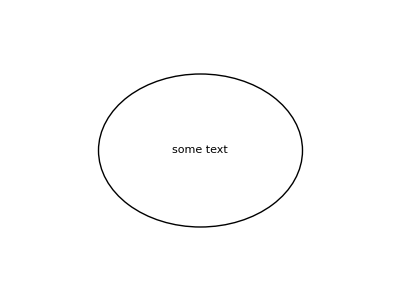
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Circle[{0,0},Scaled[0.3]],FontSize->Scaled[i],Text["some text",{0,0}]}],{i,{0.1,0.2,0.3}}]
```

ImageScaled operates relative to the whole image:

```mathematica
Framed[Graphics[Disk[ImageScaled[{.2,.2}],.2],Frame->True]]
```

-Graphics-

```mathematica
Graphics[Circle[{0,0},ImageScaled[{.5,.25}]],Frame->True]
```

-Graphics-

You can also provide coordinates in the form of offsets. Offset[{dx,dy},position] allows you to specify the position of an object by giving an absolute offset from a position that is specified in original or scaled coordinates. The units for the offset are printer's points, equal to 1/72 of an inch.

Scaled and ImageScaled can be used as wrapper around coordinate specification (and mixed with others).

```mathematica
Graphics[{Circle[{2,1.5},Scaled[0.3]],Circle[Scaled[{0.,0.5}],0.3]}]
```

-Graphics-

Of course, the above is also valid for 3-dim graphics.Whenever Mathematica draws a three-dimensional object, it always effectively puts a cuboidal box around the object. The option PlotRange specifies the range of x, y and z coordinates that Mathematica should include in the box.

Much as in two dimensions, you can use either "original" or "scaled" coordinates to specify the positions of elements in three-dimensional objects. Scaled coordinates, specified as Scaled[{sx,sy,sz}] are taken to run from 0 to 1 in each dimension. The coordinates are set up to define a right-handed coordinate system on the box.

### Lighting and Surface Properties

#### Lighting

Lighting is an option for Graphics3D and related functions that specifies what simulated lighting to use in coloring 3D surfaces. The following settings can be given: Automatic, None, Neutral, {s_1,s_2,…} (light sources s_1, s_2, …  ).

```mathematica
Graphics3D[{Sphere[]},Lighting->Automatic]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[]},Lighting->None]
```

-Graphics3D-

When specifying light sources you can chose between a number of different types: "Ambient", "Directional", "Point", and "Spot". You can place the light sources at any position and give them any color you want. Spot lights can have an opening angle of their light cone.

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Point",Red,{0,0,1.5}}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Directional",Red,{0,0,1.5}}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Spot",Red,{0,0,1.5},Pi/3}}]
```

-Graphics3D-

```mathematica
Graphics3D[{Sphere[],Sphere[{3,0,0}],Sphere[{0,3,0}],Sphere[{3,3,0}]},Lighting->{{"Point",Green,{2,2,2}}}]
```

-Graphics3D-

Lighting follows the additive color model:

```mathematica
lights={{"Spot",Red,{{3,3,5},{3,3,0}},Pi/8},{"Spot",Green,{{7,3,5},{7,3,0}},Pi/8},{"Spot",Blue,{{5,6,5},{5,6,0}},Pi/8}};
plane=ParametricPlot3D[{u,v,-2},{u,0,10},{v,0,9},PlotPoints->100,MaxRecursion->0,Mesh->None,Axes->False];
```

```mathematica
Show[plane,Lighting->lights]
```

-Graphics3D-

```mathematica
Clear[lights,plane]
```

Application: Lighting Demonstration

```mathematica
p1[θ_]:=RotationTransform[θ,{0,0,1}][{0,2,0}];
p2[θ_]:=RotationTransform[θ+Pi/2,{1,0,1}][{0,2,0}];
p3[θ_]:=RotationTransform[θ+Pi,{1,0,0}][{0,2,0}];
p4[θ_]:=RotationTransform[θ+3Pi/2,{1,0,-1}][{0,2,0}];
```

```mathematica
Animate[Graphics3D[{Specularity[White,30],Sphere[],Sphere[p1[θ],.4],Sphere[p2[θ],.4],Sphere[p3[θ],.4],Sphere[p4[θ],.4]},Lighting->{{"Ambient",GrayLevel[.1]},{"Point",Red,p1[θ]},{"Point",Green,p2[θ]},{"Point",Blue,p3[θ]},{"Point",Yellow,p4[θ]}},PlotRange->2.5,Background->Black,Boxed->False,ImageSize->300],{θ,0,2Pi},SaveDefinitions->True, AnimationRunning->False]
```

#### Specularity

Specularity[s]is a graphics directive which specifies that surfaces of 3D graphics objects which follow are to be taken to have specularity s. With specularity s a surface is taken to specularly reflect a fraction s of light that falls on it from simulated light sources.

```mathematica
Table[Graphics3D[{Orange,Specularity[n],Sphere[]}],{n,{0.2,0.5,0.7}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Specularity[s,n]uses specular exponent n.The specular exponent n defines how sharply the intensity of reflected light falls off away from the mirror-reflection direction.

```mathematica
Table[Graphics3D[{Orange,Specularity[White,n],Sphere[]}],{n,{5,20,100}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Specularity gives the surfaces a metallic appearance:

```mathematica
Graphics3D[{Table[{Specularity[White,20],RGBColor[RandomReal[1,{3}]],Sphere[RandomReal[10,{3}],RandomReal[{.5,1}]]},{50}]}]
```

-Graphics3D-

#### Glow

Glow[col] is a graphics directive which specifies that surfaces of 3D graphics objects which follow are to be taken to glow with color col. Glow is added to diffuse and specular reflection components to determine the final rendered color of a surface.

Cylinder that glows red, but has a black surface that reflects no light:

```mathematica
Graphics3D[{Glow[Red],Black,Cylinder[]}]
```

-Graphics3D-

Glow gives overall surface color that is independent of any Lighting:

```mathematica
Table[Graphics3D[{Black,Glow[Blue],Sphere[]},Lighting->{{"Point",c,{0,0,3}}}],{c,{White,Yellow,Green}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

#### Opacity

Opacity[a]is a graphics directive which specifies that graphical objects which follow are to be displayed, if possible, with opacity a. Opacity runs from 0 to 1, with 0 representing perfect transparency.  Opacity[a,color]uses the specified color with opacity a.

```mathematica
Graphics3D[{Opacity[0.5],Sphere[]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[.3],EdgeForm[Opacity[.3]],Table[Cylinder[{{0,0,0},{0,0,2r}},r],{r,1,5}]},Boxed->False]
```

-Graphics3D-

#### Colors again

We already saw how to specify colors as names or Hue directives (or as CMYKColor or GrayLevel)

Additionally there are many so called Color Schemes available in Mathematica.

There is a Color Palette available to give you an easy overview. From the menu bar choose Palettes ⊳ Color Schemes.

ColorData["scheme"] gives a function that generates colors in the named color scheme when applied to parameter values. ColorData["scheme"][par] or ColorData["scheme",par] gives the RGBColor object corresponding to parameter value par in the specified scheme.

You can also give a property:

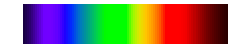

```mathematica
ColorData["VisibleSpectrum","Image"]
```

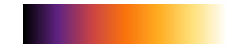

```mathematica
ColorData["SunsetColors","Panel"]
```

Typical collections of schemes include : "Gradients", "Indexed", "Named", "Physical"

Gradients

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

Color gradients have a single parameter that ranges from 0 to 1.

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[{0,1},-Graphics-]

```mathematica
ColorData["Rainbow"][1]
ColorData["Rainbow"][0]
```

RGBColor[0.857359,0.131106,0.132128]

RGBColor[0.471412,0.108766,0.527016]

The argument given to the ColorData function is automatically scaled to the range [0,1].

```mathematica
ColorData["Rainbow"][2]
```

RGBColor[0.857359,0.131106,0.132128]

```mathematica
Grid[Partition[Show[ColorData[#,"Image"],ImageSize->110]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

Indexed

Indexed color schemes use colors indexed by successive integers

```mathematica
ColorData["Indexed"]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62}

```mathematica
ColorData[1]
```

ColorDataFunction[{1,∞,1},-Graphics-]

```mathematica
ColorData[2]
```

ColorDataFunction[{1,9,1},-Graphics-]

```mathematica
ColorData[2][1]
```

RGBColor[0.858824,0.00784314,0.00784314]

If you give an argument larger than the number of indexed colors, you start over again from the beginning.

```mathematica
ColorData[2][10]
```

RGBColor[0.858824,0.00784314,0.00784314]

```mathematica
Grid[Partition[Framed[Show[ColorData[#,"Image"],ImageSize->100],FrameStyle->Gray]&/@ColorData["Indexed"],4,4,1,{}],Spacings->.25]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

Named

```mathematica
ColorData["Named"]
```

{Atoms,GeologicAges,HTML,Legacy,WebSafe}

Named schemes are sets of well-known named colors:

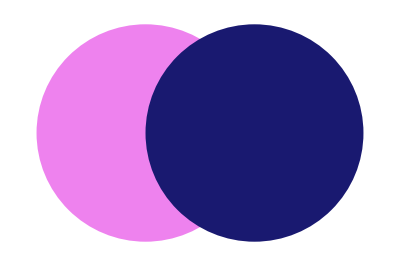

```mathematica
Graphics[{ColorData["HTML","Violet"],Disk[],ColorData["HTML","MidnightBlue"],Disk[{1,0}]}]
```

```mathematica
Grid[Partition[Framed[Show[ColorData[#,"Image"],ImageSize->100],FrameStyle->Gray]&/@ColorData["Named"],3,3,1,{}],Spacings->.25]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

Physical

Physical color schemes have different argument ranges:

```mathematica
ColorData["Physical"]
```

{BlackBodySpectrum,HypsometricTints,VisibleSpectrum}

```mathematica
ColorData["BlackBodySpectrum"]
```

ColorDataFunction[{1000,10000},-Graphics-]

```mathematica
ColorData["HypsometricTints"]
```

ColorDataFunction[{-6000,6000},-Graphics-]

```mathematica
ColorData["VisibleSpectrum"]
```

ColorDataFunction[{380,750},-Graphics-]

### GraphicsComplex

Another possibility to represent 2-D or 3-D graphics is as a GraphicsComplex. GraphicsComplex[{pt_1,pt_2,…},data] represents a graphics complex in which coordinates given as integers i in graphics primitives in data are taken to be pt_i. GraphicsComplex provides a convenient way to build up meshes or simplicial complexes in which vertices of polygons are shared.

```mathematica
v={{1,0},{0,1},{-1,0},{0,-1}};
```

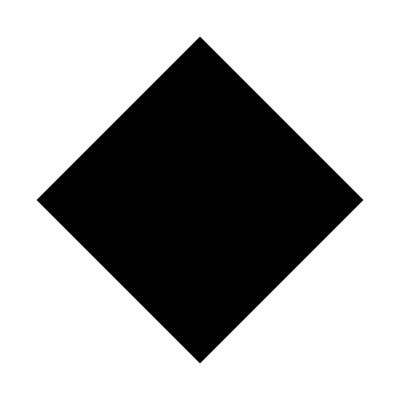
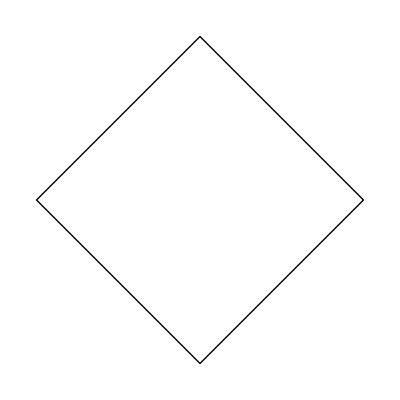

```mathematica
{Graphics[GraphicsComplex[v,Polygon[{1,2,3,4}]]],Graphics[GraphicsComplex[v,Line[{1,2,3,4,1}]]]}
```

The same in 3D

```mathematica
v={{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}};
```

```mathematica
i={{1,2,5},{2,3,5},{3,4,5},{4,1,5}};
```

```mathematica
{Graphics3D[{Opacity[.8],Yellow,GraphicsComplex[v,Polygon[i]]}],Graphics3D[{Thick,GraphicsComplex[v,Line[i]]}]}
```

{-Graphics3D-,-Graphics3D-}

A random selection of index coordinates:

```mathematica
p=Table[{Cos[2Pi/70 k],Sin[2Pi/70 k]},{k,70}];
```

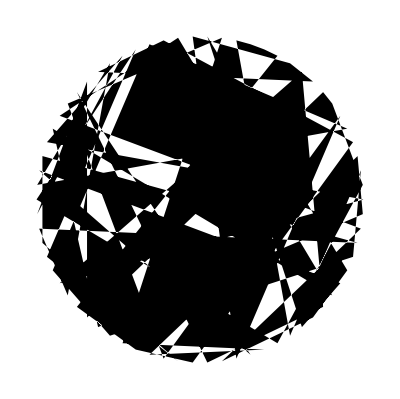

```mathematica
Graphics[GraphicsComplex[p,Polygon[RandomSample[Range[70],70]]]]
```

Here are a few more example applications. Most surface and region plots produce GraphicsComplex:

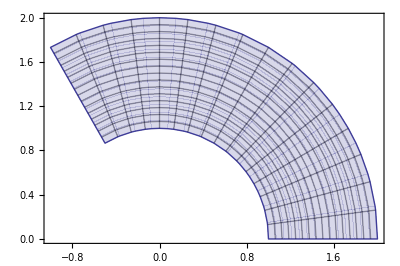

```mathematica
ParametricPlot[{r Cos[θ],r Sin[θ]},{r,1,2},{θ,0,2Pi/3},PlotRange->All]
```

You can use GraphicsComplex to transform the coordinates in this simple rotation:

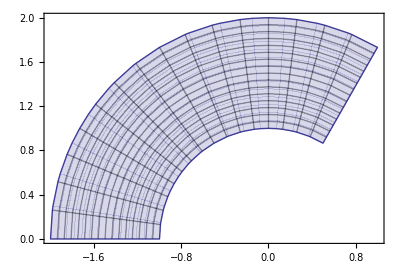

```mathematica
%/.GraphicsComplex[p_List,rest__]:>GraphicsComplex[RotationTransform[Pi/3][p],rest]
```

### Excercise

#### Pendulum

Draw a diagram to visualize an ideal physical pendulum with annotations, i.e, denote the mass, angle length etc..

#### Rainbow

Draw a rainbow.

#### Tree

Construct a function that  draws a 3-dim tree. Include parameters for position of the tree and height (and possibly width) of the tree.

#### Excercise: Zeppelin

Construct a zeppelin, fully equipped with steering flaps and gondola.

#### Let if fly...

Take you zeppelin and let it position it to fly over a forrest of Mathematica trees.